```mathematica
Quit[];
```

```mathematica
$FeynCalcStartupMessages = False;
$LoadAddOns={"FeynArtsLoader"};
<<FeynCalc`
$FAVerbose = 0;
```

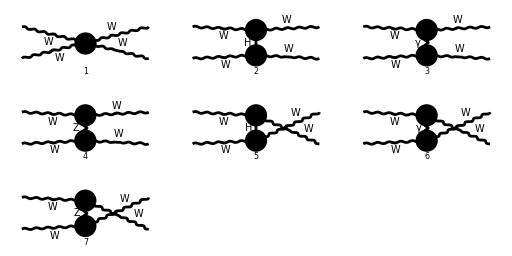

```mathematica
diagWl = InsertFields[CreateTopologies[0,2->2],{V[3],V[3]}->{V[3],V[3]},InsertionLevel->{Particles}];
FCClearScalarProducts[];
Paint[diagWl,ColumnsXRows->{3,3},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
ampW = FCFAConvert[CreateFeynAmp[diagWl],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LorentzIndexNames-> {μ,ν,ρ,σ,α,β},List->False,DropSumOver->True,SMP->True,UndoChiralSplittings->True,FinalSubstitutions->{SMP["m_Z"]->SMP["m_W"]/SMP["cos_W"]}]/.SMP["e"]->SMP["g_W"]*SMP["sin_W"]/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2] ;
```

```mathematica
ampW = ampW - ampW[[3]] -ampW[[4]]+ ampW[[3]]*Cos[α]^2 + ampW[[4]]*Cos[α]^2 + (ampW[[3]]/.SMP["m_H"]-> Subscript[M, H2])*Sin[α]^2 + (ampW[[4]]/.SMP["m_H"]-> Subscript[M, H2])*Sin[α]^2;
```

```mathematica
higgsamps = ampW[[3]] + ampW[[4]]
```

-(4 √2 cos^2(α) G_F m_W^4 (ḡ)^μσ (ḡ)^νρ ((ε̄)^*)^ρ(k1) ((ε̄)^*)^σ(k2) (ε̄)^μ(p1) (ε̄)^ν(p2))/((OverBar[k1]-OverBar[p2])^2-m_H^2)-(4 √2 cos^2(α) G_F m_W^4 (ḡ)^μρ (ḡ)^νσ ((ε̄)^*)^ρ(k1) ((ε̄)^*)^σ(k2) (ε̄)^μ(p1) (ε̄)^ν(p2))/((OverBar[k2]-OverBar[p2])^2-m_H^2)

```mathematica
FCClearScalarProducts[];
```

```mathematica
mw = SMP["m_W"];
p = Sqrt[En^2 -mw^2];
p1up = {En,0,0,p};
p1down = {En, 0, 0,-p};
p2up = {En, 0, 0, -p};
p2down = {En, 0, 0, p};
k1up = {En,p*Sin[θ],0,p*Cos[θ]};
k1down = {En,-p*Sin[θ],0,-p*Cos[θ]};
k2up = {En,-p*Sin[θ],0,-p*Cos[θ]};
k2down = {En,p*Sin[θ],0,p*Cos[θ]};
ep1up = 1/mw{p, 0, 0, En};
ep1down = 1/mw{p, 0, 0, -En};
ep2up = 1/mw{p, 0, 0, -En};
ep2down = 1/mw{p, 0, 0, En};
ek1up = 1/mw{p, En*Sin[θ], 0, En*Cos[θ]};
ek1down = 1/mw{p, -En*Sin[θ], 0, -En*Cos[θ]};
ek2up = 1/mw{p, -En*Sin[θ], 0, -En*Cos[θ]};
ek2down = 1/mw{p, En*Sin[θ], 0, En*Cos[θ]};
Rules = {Pair[Momentum[Polarization[p1,I]],Momentum[p1]] ->  ep1up.p1down,
Pair[Momentum[Polarization[p2,I]],Momentum[p2]] ->  ep2up.p2down,
 Pair[Momentum[Polarization[k2,-I]],Momentum[k2]] ->  ek2up.k2down,
 Pair[Momentum[Polarization[k1,-I]],Momentum[k1]]->  ek1up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[p2]] ->  ep1up.p2down,
Pair[Momentum[Polarization[p1,I]],Momentum[k1]] ->  ep1up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[k2]] ->  ep1up.k2down,
Pair[Momentum[Polarization[p2,I]],Momentum[p1]] ->  ep2up.p1down,
Pair[Momentum[Polarization[p2,I]],Momentum[k1]] ->  ep2up.k1down,
Pair[Momentum[Polarization[p2,I]],Momentum[k2]] ->  ep2up.k2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[p1]] ->  ek1up.p1down,
Pair[Momentum[Polarization[k1,-I]],Momentum[p2]] ->  ek1up.p2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[k2]] ->  ek1up.k2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[p1]] ->  ek2up.p1down,
Pair[Momentum[Polarization[k2,-I]],Momentum[p2]] ->  ek2up.p2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[k1]] ->  ek2up.k1down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[p1,I]]] ->  ep1up.ep1down,Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[p2,I]]] ->  ep1up.ep2down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[k1,-I]]] ->  ep1up.ek1down,
Pair[Momentum[Polarization[p1,I]],Momentum[Polarization[k2,-I]]] ->  ep1up.ek2down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[p2,I]]] ->  ep2up.ep2down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[k1,-I]]] ->  ep2up.ek1down,
Pair[Momentum[Polarization[p2,I]],Momentum[Polarization[k2,-I]]] ->  ep2up.ek2down,
Pair[Momentum[Polarization[k1,-I]],Momentum[Polarization[k1,-I]]] ->  ek1up.ek1down,
Pair[Momentum[Polarization[k1,-I]],Momentum[Polarization[k2,-I]]] ->  ek1up.ek2down,
Pair[Momentum[Polarization[k2,-I]],Momentum[Polarization[k2,-I]]] ->  ek2up.ek2down};
SP[p1,p1] =SMP["m_W"]^2;
SP[p2,p2] =SMP["m_W"]^2;
SP[k1,k1] =SMP["m_W"]^2;
SP[k2,k2] =SMP["m_W"]^2;
SP[p1,p2] =(2 En^2- SMP["m_W"]^2);
SP[p1,k1] =(En^2- (En^2-SMP["m_W"]^2)Cos[θ]);
SP[p1,k2] =(En^2+ (En^2-SMP["m_W"]^2)Cos[θ]);
SP[p2,k1] =(En^2+ (En^2-SMP["m_W"]^2)Cos[θ]);
SP[p2,k2] =(En^2- (En^2-SMP["m_W"]^2)Cos[θ]);SP[k1,k2] =(2 En^2- SMP["m_W"]^2);
```

```mathematica
three = ampW[[3]]//Contract//Simplify;
four = ampW[[4]]//Contract//Simplify;
```

```mathematica
threelong = three/.Rules//Simplify;
```

```mathematica
fourlong = four/.Rules//Simplify;
```

```mathematica
threelong = threelong//FeynAmpDenominatorExplicit;
fourlong = fourlong//FeynAmpDenominatorExplicit;
```

```mathematica
threelong = threelong/.En->Sqrt[S]/2;
fourlong = fourlong/.En->Sqrt[S]/2;
```

```mathematica
threelong = threelong/.SMP["m_H"]-> x*S//Simplify
```

(cos^2(α) G_F (-4 m_W^2+S cos(θ)+S)^2)/(√2 (S (cos(θ)+2 S x^2+1)-4 (cos(θ)+1) m_W^2))

```mathematica
amp1 = Series[threelong,{x, ∞,2}]//Simplify
```

(cos^2(α) G_F (-4 m_W^2+S cos(θ)+S)^2)/(2 √2 S^2 x^2)+O((1/x)^3)

```mathematica
%//Expand//Simplify
```

(cos^2(α) G_F (-4 m_W^2+S cos(θ)+S)^2)/(2 √2 S^2 x^2)+O((1/x)^3)

```mathematica
amp2 = Series[fourlong,{SMP["m_H"], ∞,2}]//Simplify
```

(4 √2 cos^2(α) G_F (m_W^2+1/4 S (cos(θ)-1))^2)/m_H^2+O((1/m_H)^3)

```mathematica
amp1 + amp2//Simplify
```

(cos^2(α) G_F (-8 S m_W^2+16 m_W^4+S^2 (cos^2(θ)+1)))/(√2 m_H^2)+O((1/m_H)^3)

```mathematica
higgsamps = higgsamps//Contract//Simplify;
```

-4 √2 G_F m_W^4 ((((ε̄)^*(k1)·ε̄(p2)) ((ε̄)^*(k2)·ε̄(p1)))/((OverBar[k1]-OverBar[p2])^2-m_H^2)+(((ε̄)^*(k1)·ε̄(p1)) ((ε̄)^*(k2)·ε̄(p2)))/((OverBar[k2]-OverBar[p2])^2-m_H^2))

```mathematica
higgsamplong = higgsamps/.Rules//Simplify
```

-4 √2 G_F (((m_W^2-En^2 (cos(θ)+1))^2)/((OverBar[k1]-OverBar[p2])^2-m_H^2)+((En^2 (cos(θ)-1)+m_W^2)^2)/((OverBar[k2]-OverBar[p2])^2-m_H^2))

```mathematica
higgsamplong = higgsamplong//FeynAmpDenominatorExplicit
```

-4 √2 G_F (((En^2 (cos(θ)-1)+m_W^2)^2)/(2 En^2 cos(θ)-2 En^2-m_H^2-2 cos(θ) m_W^2+2 m_W^2)+((m_W^2-En^2 (cos(θ)+1))^2)/(-2 En^2 cos(θ)-2 En^2-m_H^2+2 cos(θ) m_W^2+2 m_W^2))

```mathematica
higgsA = higgsamplong/.En->(√S)/2
```

-4 √2 G_F (((m_W^2+1/4 S (cos(θ)-1))^2)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2+1/2 S cos(θ)-S/2)+((m_W^2-1/4 S (cos(θ)+1))^2)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-1/2 S cos(θ)-S/2))

```mathematica
Series[higgsA, {SMP["m_H"],∞,2}]
```

(G_F (-8 S m_W^2+16 m_W^4+S^2 cos^2(θ)+S^2))/(√2 m_H^2)+O((1/m_H)^3)

```mathematica
ampW= ampW//Contract//Simplify;
```

```mathematica
ampWlong = ampW/.Rules//Simplify;
```

```mathematica
ampWlong = ampWlong//FeynAmpDenominatorExplicit;
```

```mathematica
a = ampWlong/.En->(√S)/2;
```

```mathematica
Series[a, {Subscript[M, H2],∞,2}]
```

1/(√2 m_W^2)G_F (-(16 cos(θ) (sin(θ_W))^2 m_W^6)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(16 (sin(θ_W))^2 m_W^6)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(16 cos(θ) (sin(θ_W))^2 m_W^6)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(16 (sin(θ_W))^2 m_W^6)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 cos(2 α) m_W^6)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(4 m_W^6)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(4 cos(2 α) m_W^6)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 m_W^6)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(24 S (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(28 S cos(θ) (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(20 S cos(2 θ) (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(24 S (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(28 S cos(θ) (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(20 S cos(2 θ) (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(2 S cos(2 α) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(S cos(2 α-θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(2 S cos(θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(S cos(2 α+θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(2 S m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S cos(2 α) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(S cos(2 α-θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S cos(θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(S cos(2 α+θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(15 S^2 (sin(θ_W))^2 m_W^2)/(2 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(49 S^2 cos(θ) (sin(θ_W))^2 m_W^2)/(4 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(9 S^2 cos(2 θ) (sin(θ_W))^2 m_W^2)/(2 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(3 θ) (sin(θ_W))^2 m_W^2)/(4 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(15 S^2 (sin(θ_W))^2 m_W^2)/(2 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(49 S^2 cos(θ) (sin(θ_W))^2 m_W^2)/(4 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(9 S^2 cos(2 θ) (sin(θ_W))^2 m_W^2)/(2 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(S^2 cos(3 θ) (sin(θ_W))^2 m_W^2)/(4 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-8 S m_W^2-(3 S^2 m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(3 S^2 cos(2 α) m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 (α-θ)) m_W^2)/(16 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(2 α-θ) m_W^2)/(4 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(θ) m_W^2)/(2 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 θ) m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 (α+θ)) m_W^2)/(16 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(2 α+θ) m_W^2)/(4 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(3 S^2 m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(3 S^2 cos(2 α) m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 (α-θ)) m_W^2)/(16 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 α-θ) m_W^2)/(4 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(θ) m_W^2)/(2 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 θ) m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 (α+θ)) m_W^2)/(16 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 α+θ) m_W^2)/(4 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(5 S^2)/2+(7 S^3 (sin(θ_W))^2)/(8 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(17 S^3 cos(θ) (sin(θ_W))^2)/(16 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^3 cos(2 θ) (sin(θ_W))^2)/(8 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^3 cos(3 θ) (sin(θ_W))^2)/(16 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(7 S^3 (sin(θ_W))^2)/(8 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(17 S^3 cos(θ) (sin(θ_W))^2)/(16 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(S^3 cos(2 θ) (sin(θ_W))^2)/(8 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^3 cos(3 θ) (sin(θ_W))^2)/(16 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-1/2 S^2 cos(2 θ)+(16 (cos(θ_W))^2 ((cos(θ)-1) m_W^6+1/4 S (7 cos(θ)+5 cos(2 θ)+6) m_W^4+1/16 S^2 cos^2(θ/2) (-20 cos(θ)+cos(2 θ)-5) m_W^2-1/16 S^3 cos^4(θ/2) (cos(θ)-3)))/(2 cos(θ) m_W^2-m_W^2/(cos(θ_W))^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 (cos(θ_W))^2 (4 (cos(θ)+1) m_W^6-S (-7 cos(θ)+5 cos(2 θ)+6) m_W^4-1/4 S^2 (20 cos(θ)+cos(2 θ)-5) sin^2(θ/2) m_W^2-1/4 S^3 (cos(θ)+3) sin^4(θ/2)))/(-2 cos(θ) m_W^2-m_W^2/(cos(θ_W))^2+2 m_W^2-S/2+1/2 S cos(θ)))-(G_F (-32 S cos(2 α) m_W^2+32 S m_W^2+64 cos(2 α) m_W^4-64 m_W^4+S^2 cos(2 (α-θ))+S^2 cos(2 (α+θ))+6 S^2 cos(2 α)-2 S^2 cos(2 θ)-6 S^2))/(8 √2 M_H2^2)+O((1/M_H2)^3)

```mathematica
Series[a, {Subscript[M, H2],∞,4}]
```

1/(√2 m_W^2)G_F (-(16 cos(θ) (sin(θ_W))^2 m_W^6)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(16 (sin(θ_W))^2 m_W^6)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(16 cos(θ) (sin(θ_W))^2 m_W^6)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(16 (sin(θ_W))^2 m_W^6)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 cos(2 α) m_W^6)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(4 m_W^6)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(4 cos(2 α) m_W^6)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 m_W^6)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(24 S (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(28 S cos(θ) (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(20 S cos(2 θ) (sin(θ_W))^2 m_W^4)/(-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(24 S (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(28 S cos(θ) (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(20 S cos(2 θ) (sin(θ_W))^2 m_W^4)/(2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(2 S cos(2 α) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(S cos(2 α-θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(2 S cos(θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))-(S cos(2 α+θ) m_W^4)/(-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ))+(2 S m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S cos(2 α) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(S cos(2 α-θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(2 S cos(θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))+(S cos(2 α+θ) m_W^4)/(-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ))-(15 S^2 (sin(θ_W))^2 m_W^2)/(2 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(49 S^2 cos(θ) (sin(θ_W))^2 m_W^2)/(4 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(9 S^2 cos(2 θ) (sin(θ_W))^2 m_W^2)/(2 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(3 θ) (sin(θ_W))^2 m_W^2)/(4 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(15 S^2 (sin(θ_W))^2 m_W^2)/(2 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(49 S^2 cos(θ) (sin(θ_W))^2 m_W^2)/(4 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(9 S^2 cos(2 θ) (sin(θ_W))^2 m_W^2)/(2 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(S^2 cos(3 θ) (sin(θ_W))^2 m_W^2)/(4 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-8 S m_W^2-(3 S^2 m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(3 S^2 cos(2 α) m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 (α-θ)) m_W^2)/(16 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(2 α-θ) m_W^2)/(4 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(θ) m_W^2)/(2 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 θ) m_W^2)/(8 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(S^2 cos(2 (α+θ)) m_W^2)/(16 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^2 cos(2 α+θ) m_W^2)/(4 (-m_H^2-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(3 S^2 m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(3 S^2 cos(2 α) m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 (α-θ)) m_W^2)/(16 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 α-θ) m_W^2)/(4 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(θ) m_W^2)/(2 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 θ) m_W^2)/(8 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 (α+θ)) m_W^2)/(16 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^2 cos(2 α+θ) m_W^2)/(4 (-m_H^2+2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(5 S^2)/2+(7 S^3 (sin(θ_W))^2)/(8 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))-(17 S^3 cos(θ) (sin(θ_W))^2)/(16 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^3 cos(2 θ) (sin(θ_W))^2)/(8 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(S^3 cos(3 θ) (sin(θ_W))^2)/(16 (-2 cos(θ) m_W^2+2 m_W^2-S/2+1/2 S cos(θ)))+(7 S^3 (sin(θ_W))^2)/(8 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(17 S^3 cos(θ) (sin(θ_W))^2)/(16 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))+(S^3 cos(2 θ) (sin(θ_W))^2)/(8 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-(S^3 cos(3 θ) (sin(θ_W))^2)/(16 (2 cos(θ) m_W^2+2 m_W^2-S/2-1/2 S cos(θ)))-1/2 S^2 cos(2 θ)+(16 (cos(θ_W))^2 ((cos(θ)-1) m_W^6+1/4 S (7 cos(θ)+5 cos(2 θ)+6) m_W^4+1/16 S^2 cos^2(θ/2) (-20 cos(θ)+cos(2 θ)-5) m_W^2-1/16 S^3 cos^4(θ/2) (cos(θ)-3)))/(2 cos(θ) m_W^2-m_W^2/(cos(θ_W))^2+2 m_W^2-S/2-1/2 S cos(θ))-(4 (cos(θ_W))^2 (4 (cos(θ)+1) m_W^6-S (-7 cos(θ)+5 cos(2 θ)+6) m_W^4-1/4 S^2 (20 cos(θ)+cos(2 θ)-5) sin^2(θ/2) m_W^2-1/4 S^3 (cos(θ)+3) sin^4(θ/2)))/(-2 cos(θ) m_W^2-m_W^2/(cos(θ_W))^2+2 m_W^2-S/2+1/2 S cos(θ)))-(G_F (-32 S cos(2 α) m_W^2+32 S m_W^2+64 cos(2 α) m_W^4-64 m_W^4+S^2 cos(2 (α-θ))+S^2 cos(2 (α+θ))+6 S^2 cos(2 α)-2 S^2 cos(2 θ)-6 S^2))/(8 √2 M_H2^2)+1/(16 √2 M_H2^4)G_F (-4 S^2 m_W^2 cos(2 (α-θ))-32 S^2 cos(θ) m_W^2 cos(2 α-θ)-4 S^2 m_W^2 cos(2 (α+θ))-32 S^2 cos(θ) m_W^2 cos(2 α+θ)-56 S^2 cos(2 α) m_W^2+64 S^2 cos^2(θ) m_W^2+8 S^2 cos(2 θ) m_W^2+56 S^2 m_W^2+64 S cos(θ) m_W^4 cos(2 α-θ)+64 S cos(θ) m_W^4 cos(2 α+θ)+192 S cos(2 α) m_W^4-128 S cos^2(θ) m_W^4-192 S m_W^4-256 cos(2 α) m_W^6+256 m_W^6+S^3 cos(2 (α-θ))+4 S^3 cos(θ) cos(2 α-θ)+S^3 cos(2 (α+θ))+4 S^3 cos(θ) cos(2 α+θ)+6 S^3 cos(2 α)-8 S^3 cos^2(θ)-2 S^3 cos(2 θ)-6 S^3)+O((1/M_H2)^5)

```mathematica
Heavyhiggscont = SMP["G_F"] 1/(8 Subscript[M, H2]^2 2^(1/2))(-32*S*Cos[2α] SMP["m_W"]^2 + 32*S*SMP["m_W"]^2 + 64Cos[2α] SMP["m_W"]^4 - 64 SMP["m_W"]^4 + S^2 Cos[2(α-θ)] + S^2 Cos[2(α + θ)] + 6 S^2 Cos[2α] - 2 S^2 Cos[2θ] - 6 S^2)//Simplify
```

-(sin^2(α) G_F (-16 S m_W^2+32 m_W^4+S^2 (cos(2 θ)+3)))/(2 √2 M_H2^2)

```mathematica
S2 = Limit[a/S^2/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]],S-> ∞]//Simplify
```

0

```mathematica
S1 = Limit[(a -S2*S*S)/S/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]],S->∞]
```

0

```mathematica
S0 = Limit[(a - S2*S*S - S1 *S)/.SMP["sin_W"]->Sin[Subscript[θ, W]]/.SMP["cos_W"]->Cos[Subscript[θ, W]]/.SMP["m_Z"]->mw/Cos[Subscript[θ, W]], S-> ∞]//Simplify
```

-√2 G_F csc^2(θ) (2 cos^2(α) sin^2(θ) m_H^2+2 sin^2(α) sin^2(θ) M_H2^2+(cos(2 θ)+7) m_W^2 sec^2(θ_W))

```mathematica
ampSquared = (ampWlong ComplexConjugate[ampWlong])/.En->Sqrt[S]/2;
```

```mathematica
dsig = 1/(64 π^2 S)*ampSquared/.SMP["m_H"]->125.1/.SMP["m_W"]-> 80.379/.SMP["cos_W"]->80.379/91.1876/.SMP["sin_W"]->Sqrt[1-(80.379/91.1876)^2]/.SMP["G_F"]-> 1.1663787*10^-5/.SMP["m_Z"]->91.1876;
```

```mathematica
(*MH = 5000 GeV*)
AbsoluteTiming[xs = Range[200,10000,50];
ys = Table[NIntegrate[(dsig*2π*Sin[θ])/.α-> .2/.Subscript[M, H2]->5000/.θ->y/.S->SqrtS^2/.SqrtS-> x ,{y,0.01,3.1},Method->{Automatic,"SymbolicProcessing"->0}, MaxRecursion->200],{x,xs}];
];
(*MH = 2000 GeV*)
AbsoluteTiming[xs = Range[200,10000,50];
y2s = Table[NIntegrate[(dsig*2π*Sin[θ])/.α-> .2/.Subscript[M, H2]->2000/.θ->y/.S->SqrtS^2/.SqrtS-> x ,{y,0.01,3.1},Method->{Automatic,"SymbolicProcessing"->0}, MaxRecursion->200],{x,xs}];
];
(*SM cross section*)
AbsoluteTiming[xs = Range[200,10000,50];
sm = Table[NIntegrate[(dsig*2π*Sin[θ])/.α-> 0/.Subscript[M, H2]->2000/.θ->y/.S->SqrtS^2/.SqrtS-> x ,{y,0.01,3.1},Method->{Automatic,"SymbolicProcessing"->0}, MaxRecursion->200],{x,xs}];
];
```

```mathematica
data = Transpose@{xs,ys};
data2 = Transpose@{xs,y2s};
s1 = ListLogPlot[data, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotStyle->Blue,PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",.2,5000]}];
s2 = ListLogPlot[data2, PlotLabel->"σ_Singlet/σ_SM vs √s (GeV)",PlotStyle->Red,PlotLegends->{StringForm["Sin[α] = ``, M_Heavy = `` GeV",.2,2000]}];
```

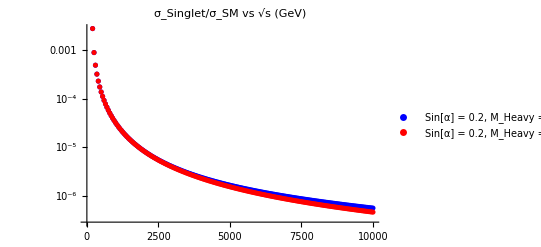

```mathematica
Show[s1,s2]
```